```mathematica
check[l_,fname_,f_]:=Module[{α=-1/2,β=l-1/2,data,x,norm,normtmp,tmp,exact,error,relError,plotValue,plotError,plotRelError},data = Import[fname<>ToString[l]<>".dat"];x = data[[;;,1]];
norm[k_]:=If[k==0,√(1/2(Gamma[α+1]Gamma[β+1])/Gamma[α+β+2]),√(1/(2(2k+α+β+1))(Gamma[k+α+1]Gamma[k+β+1])/(Gamma[k+α+β+1]Gamma[k+1]))];
normtmp = Table[norm[i],{i,0,Dimensions[data][[2]]-3}];
tmp = Table[Table[f[i,l,x[[j]]]/normtmp[[i+1]],{i,0,Dimensions[data][[2]]-3}],{j,1,Dimensions[data][[1]]}];
exact=Transpose[Join[{x},Transpose@tmp]];
error = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]],{i,2,Dimensions[exact][[2]]}];
relError = Table[Max[Abs[exact[[;;,i]]-data[[;;,i+1]]]/Abs[exact[[;;,i]]]],{i,2,Dimensions[exact][[2]]}];
Print[error];
Print[relError];
plotValue =ListPlot[data[[;;,{1,Floor[Dimensions[data][[2]]/2]}]],Joined->True,Mesh->All];
plotError=ListLogPlot[error];
plotRelError=ListLogPlot[relError];
Print[GraphicsGrid[{{plotValue,plotError,plotRelError}},ImageSize->1000]];
];
```

```mathematica
mc = 1;
```

{6.66134×10^-16,8.88178×10^-16,1.11022×10^-15,1.33227×10^-15,1.77636×10^-15,2.44249×10^-15,2.88658×10^-15,3.77476×10^-15,3.94129×10^-15,5.10703×10^-15,5.88418×10^-15,6.99441×10^-15,8.21565×10^-15,9.21485×10^-15,1.02696×10^-14,1.12688×10^-14,1.22402×10^-14,1.317×10^-14,1.40166×10^-14,1.48492×10^-14,1.54321×10^-14,1.65423×10^-14,1.76525×10^-14,1.88738×10^-14,2.02061×10^-14,2.19824×10^-14,2.34257×10^-14,2.4758×10^-14,2.57572×10^-14,2.69784×10^-14,2.81997×10^-14,2.9643×10^-14,3.13083×10^-14,3.27516×10^-14,3.40838×10^-14,3.54161×10^-14,3.67484×10^-14,3.79696×10^-14,3.9968×10^-14,4.13003×10^-14,4.35207×10^-14,4.4631×10^-14,4.61853×10^-14,4.64073×10^-14,4.86278×10^-14,4.90719×10^-14,5.10703×10^-14,5.28466×10^-14,5.32907×10^-14,5.41789×10^-14,5.63993×10^-14,5.77316×10^-14,5.9508×10^-14,6.08402×10^-14,6.28386×10^-14,6.4615×10^-14,6.66134×10^-14,6.72795×10^-14,6.92779×10^-14,6.99441×10^-14,7.16094×10^-14,7.32747×10^-14,7.49401×10^-14,7.72715×10^-14,7.93809×10^-14,8.12683×10^-14,8.35998×10^-14,8.60423×10^-14,8.87068×10^-14,9.09273×10^-14,9.31477×10^-14,9.54792×10^-14,9.75886×10^-14,9.99201×10^-14,1.01696×10^-13,1.03806×10^-13,1.05915×10^-13,1.07692×10^-13,1.09579×10^-13,1.11799×10^-13,1.14131×10^-13,1.16462×10^-13,1.19238×10^-13,1.21458×10^-13,1.23679×10^-13,1.26232×10^-13,1.28231×10^-13,1.31117×10^-13,1.3356×10^-13,1.36113×10^-13,1.38445×10^-13,1.41109×10^-13,1.43663×10^-13,1.46438×10^-13,1.49214×10^-13,1.51767×10^-13,1.53988×10^-13,1.56097×10^-13,1.5854×10^-13,1.60982×10^-13,1.63092×10^-13,1.65312×10^-13,1.68421×10^-13,1.71085×10^-13,1.74416×10^-13,1.77525×10^-13,1.81188×10^-13,1.84519×10^-13,1.88183×10^-13,1.91736×10^-13,1.95732×10^-13,1.99618×10^-13,2.03282×10^-13,2.07057×10^-13,2.10387×10^-13,2.13718×10^-13,2.17382×10^-13,2.20712×10^-13,2.23821×10^-13,2.27374×10^-13,2.30371×10^-13,2.34146×10^-13,2.37588×10^-13,2.4114×10^-13,2.44693×10^-13,2.48246×10^-13,2.51466×10^-13,2.55018×10^-13}

{7.0108×10^-16,8.56306×10^-16,2.99252×10^-14,1.62253×10^-14,2.54556×10^-13,7.25126×10^-14,4.00526×10^-14,3.10776×10^-14,1.88759×10^-13,1.30241×10^-13,1.4515×10^-13,1.07042×10^-13,1.9835×10^-13,1.96053×10^-13,4.5751×10^-13,1.48069×10^-13,9.35578×10^-14,4.16156×10^-13,5.05084×10^-13,8.90852×10^-14,2.48932×10^-13,1.95677×10^-13,1.81097×10^-13,3.39536×10^-13,4.40033×10^-14,2.44773×10^-13,3.01362×10^-13,4.36409×10^-13,5.86035×10^-13,2.34395×10^-12,2.15094×10^-13,1.48878×10^-13,1.33704×10^-13,1.73435×10^-13,8.49991×10^-13,1.54502×10^-12,2.38824×10^-13,1.40687×10^-12,3.0828×10^-13,7.66051×10^-13,4.60909×10^-13,2.58908×10^-13,2.31729×10^-13,1.66775×10^-12,1.24113×10^-13,1.58745×10^-13,3.08652×10^-13,1.09726×10^-13,1.28105×10^-13,3.43011×10^-13,5.50506×10^-13,4.24461×10^-13,3.43362×10^-13,3.45674×10^-12,2.45422×10^-13,6.14587×10^-13,6.54054×10^-13,2.80645×10^-13,2.68756×10^-13,3.15323×10^-13,4.48293×10^-13,4.78278×10^-13,1.98677×10^-12,9.9885×10^-13,2.17977×10^-12,1.08531×10^-11,1.54359×10^-12,8.26827×10^-13,2.41186×10^-12,4.2488×10^-13,3.40472×10^-13,4.75458×10^-13,5.5611×10^-13,2.09047×10^-13,1.98286×10^-13,4.85592×10^-13,1.74372×10^-12,6.37062×10^-13,5.66891×10^-12,6.29594×10^-13,3.0758×10^-13,4.59351×10^-13,1.41282×10^-12,3.69673×10^-13,3.63095×10^-13,3.11647×10^-13,8.00216×10^-13,1.22106×10^-12,5.24919×10^-12,3.57815×10^-13,3.78017×10^-12,1.11778×10^-12,3.95403×10^-13,5.72684×10^-13,3.04114×10^-13,1.50758×10^-12,2.77298×10^-13,1.9486×10^-13,1.99501×10^-13,1.8404×10^-12,1.34874×10^-12,6.27962×10^-13,6.47612×10^-13,1.16557×10^-12,1.05968×10^-11,5.3687×10^-12,8.30746×10^-13,4.33077×10^-13,8.18499×10^-13,5.7232×10^-13,4.66637×10^-13,1.45962×10^-12,1.51641×10^-12,8.33436×10^-12,4.5661×10^-13,6.96663×10^-13,1.37142×10^-12,1.55252×10^-11,1.77168×10^-12,1.27604×10^-12,3.89688×10^-12,1.10101×10^-12,3.78992×10^-13,1.0541×10^-12,1.00095×10^-12,1.47916×10^-12,1.20323×10^-12,6.10561×10^-13}

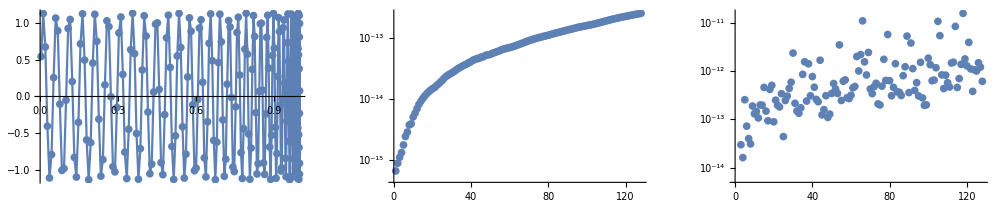

```mathematica
poly[k_,m_,y_]:=y^m JacobiP[k,-1/2,m-1/2,2 y^2-1];
check[mc,"worland_poly_l",poly];
```

{4.44089×10^-16,1.33227×10^-15,2.66454×10^-15,6.21725×10^-15,1.24345×10^-14,1.59872×10^-14,2.22045×10^-14,2.4869×10^-14,3.19744×10^-14,5.32907×10^-14,7.81597×10^-14,7.81597×10^-14,1.10134×10^-13,1.45661×10^-13,1.91847×10^-13,2.34479×10^-13,2.84217×10^-13,3.41061×10^-13,3.90799×10^-13,4.47642×10^-13,4.9738×10^-13,5.18696×10^-13,5.82645×10^-13,6.25278×10^-13,6.53699×10^-13,7.10543×10^-13,7.60281×10^-13,7.95808×10^-13,8.2423×10^-13,8.52651×10^-13,8.81073×10^-13,8.81073×10^-13,8.95284×10^-13,9.23706×10^-13,9.23706×10^-13,9.66338×10^-13,1.03739×10^-12,1.10845×10^-12,1.13687×10^-12,1.1795×10^-12,1.19371×10^-12,1.22213×10^-12,1.20792×10^-12,1.16529×10^-12,1.20792×10^-12,1.1795×10^-12,1.22213×10^-12,1.22213×10^-12,1.22213×10^-12,1.22213×10^-12,1.23634×10^-12,1.26477×10^-12,1.26477×10^-12,1.27898×10^-12,1.25056×10^-12,1.25056×10^-12,1.25056×10^-12,1.25056×10^-12,1.25056×10^-12,1.22213×10^-12,1.20792×10^-12,1.25056×10^-12,1.25056×10^-12,1.27898×10^-12,1.33582×10^-12,1.33582×10^-12,1.53477×10^-12,1.76215×10^-12,2.01794×10^-12,2.18847×10^-12,2.38742×10^-12,2.58638×10^-12,2.84217×10^-12,3.12639×10^-12,3.18323×10^-12,3.41061×10^-12,3.58114×10^-12,3.75167×10^-12,3.95062×10^-12,4.12115×10^-12,4.17799×10^-12,4.3201×10^-12,4.63274×10^-12,4.68958×10^-12,4.80327×10^-12,4.9738×10^-12,5.03064×10^-12,5.28644×10^-12,5.42855×10^-12,5.54223×10^-12,5.76961×10^-12,6.13909×10^-12,6.48015×10^-12,6.87805×10^-12,7.19069×10^-12,7.53175×10^-12,7.5886×10^-12,7.90124×10^-12,8.15703×10^-12,8.52651×10^-12,8.78231×10^-12,9.18021×10^-12,9.57812×10^-12,9.89075×10^-12,1.02887×10^-11,1.0715×10^-11,1.1255×10^-11,1.17382×10^-11,1.22213×10^-11,1.26477×10^-11,1.32445×10^-11,1.38982×10^-11,1.45519×10^-11,1.51203×10^-11,1.5774×10^-11,1.62004×10^-11,1.68541×10^-11,1.74225×10^-11,1.79909×10^-11,1.87299×10^-11,1.92415×10^-11,2.01226×10^-11,2.08331×10^-11,2.16289×10^-11,2.24532×10^-11,2.33626×10^-11,2.44142×10^-11,2.54943×10^-11}

{3.93564×10^-16,6.87969×10^-16,9.60115×10^-15,1.5472×10^-14,2.00387×10^-13,6.5331×10^-14,3.26895×10^-14,2.04766×10^-14,1.42101×10^-13,7.94271×10^-14,2.02666×10^-13,4.37042×10^-14,3.04701×10^-13,5.92339×10^-13,4.64655×10^-13,7.98263×10^-14,7.47885×10^-14,2.26495×10^-13,1.24887×10^-13,6.53792×10^-14,2.90248×10^-13,5.60884×10^-13,2.89426×10^-13,3.09013×10^-13,1.30067×10^-13,2.2066×10^-13,3.27497×10^-13,1.01609×10^-12,1.04743×10^-12,2.36562×10^-12,2.35442×10^-13,1.60694×10^-13,1.27579×10^-13,1.32348×10^-13,9.53415×10^-13,1.27619×10^-12,1.92887×10^-13,1.34659×10^-12,2.09132×10^-13,5.23853×10^-13,7.5635×10^-13,1.35246×10^-13,3.14281×10^-13,3.70001×10^-12,2.17229×10^-13,2.06044×10^-13,1.42743×10^-13,9.54847×10^-13,1.21351×10^-13,4.02235×10^-13,5.40954×10^-13,3.27848×10^-13,2.46775×10^-13,2.3457×10^-12,2.67469×10^-13,4.22294×10^-13,4.59879×10^-13,3.06991×10^-13,3.40931×10^-13,2.83102×10^-13,3.4005×10^-13,4.2466×10^-13,1.79091×10^-12,8.73699×10^-13,1.90522×10^-12,9.43803×10^-12,1.3352×10^-12,7.11627×10^-13,2.65277×10^-12,3.61398×10^-13,2.8804×10^-13,3.92125×10^-13,2.38967×10^-13,1.75244×10^-13,2.29589×10^-13,8.68077×10^-13,8.37319×10^-13,1.87551×10^-12,1.03023×10^-11,9.65374×10^-13,5.20646×10^-13,4.56635×10^-13,1.83611×10^-12,3.50679×10^-13,3.71281×10^-13,3.54929×10^-13,9.29733×10^-13,1.44707×10^-12,4.06184×10^-12,2.54231×10^-13,2.0735×10^-13,1.11921×10^-12,2.68775×10^-13,6.02797×10^-13,4.35229×10^-13,6.81976×10^-13,3.6715×10^-13,2.33248×10^-13,2.36941×10^-13,1.95126×10^-12,4.6051×10^-13,6.36224×10^-13,5.36406×10^-13,1.25344×10^-12,1.00997×10^-11,9.76173×10^-12,7.50405×10^-13,4.0789×10^-13,1.5588×10^-12,1.05464×10^-12,5.14654×10^-13,3.01814×10^-13,1.24363×10^-12,5.38623×10^-12,4.12851×10^-13,6.2513×10^-13,1.22241×10^-12,1.37532×10^-11,1.56056×10^-12,7.53672×10^-13,2.73947×10^-12,1.13465×10^-12,3.71551×10^-13,9.95262×10^-13,1.61342×10^-12,9.87609×10^-13,1.10731×10^-12,4.14818×10^-13}

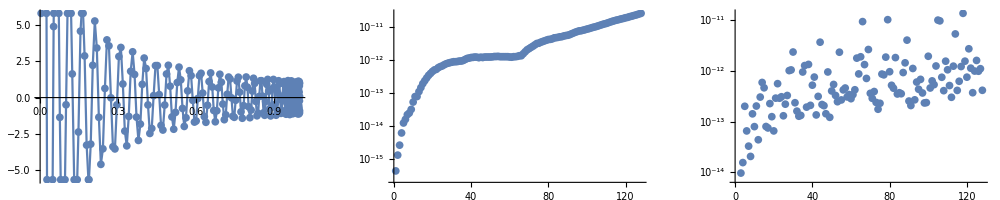

```mathematica
divr[k_,m_,y_]:=y^(m-1)JacobiP[k,-1/2,m-1/2,2 y^2-1];
check[mc,"worland_divr_l",divr];
```

```mathematica
D[y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}];
```

{4.44089×10^-16,5.32907×10^-15,1.06581×10^-14,2.13163×10^-14,8.52651×10^-14,2.27374×10^-13,2.27374×10^-13,4.26326×10^-13,7.95808×10^-13,1.02318×10^-12,1.42109×10^-12,1.93268×10^-12,2.72848×10^-12,3.86535×10^-12,5.34328×10^-12,7.50333×10^-12,9.32232×10^-12,1.18234×10^-11,1.45519×10^-11,1.7053×10^-11,2.00089×10^-11,2.31921×10^-11,2.72848×10^-11,3.16049×10^-11,3.68345×10^-11,4.11546×10^-11,4.82032×10^-11,5.36602×10^-11,6.23004×10^-11,7.41238×10^-11,8.6402×10^-11,9.86802×10^-11,1.10049×10^-10,1.17325×10^-10,1.27329×10^-10,1.33696×10^-10,1.40972×10^-10,1.48248×10^-10,1.54614×10^-10,1.63709×10^-10,1.72804×10^-10,1.7917×10^-10,1.88265×10^-10,1.9736×10^-10,2.04636×10^-10,2.11912×10^-10,2.18279×10^-10,2.27374×10^-10,2.3465×10^-10,2.41926×10^-10,2.45564×10^-10,2.49202×10^-10,2.5284×10^-10,2.56478×10^-10,2.67391×10^-10,2.76486×10^-10,2.80124×10^-10,2.874×10^-10,2.92857×10^-10,3.01952×10^-10,3.09228×10^-10,3.21961×10^-10,3.4197×10^-10,3.69255×10^-10,3.92902×10^-10,4.20187×10^-10,4.40195×10^-10,4.65661×10^-10,5.00222×10^-10,5.16593×10^-10,5.49335×10^-10,5.7662×10^-10,5.98448×10^-10,6.16637×10^-10,6.34827×10^-10,6.49379×10^-10,6.4756×10^-10,6.60293×10^-10,6.78483×10^-10,6.98492×10^-10,7.22139×10^-10,7.3851×10^-10,7.65795×10^-10,7.82165×10^-10,8.11269×10^-10,8.36735×10^-10,8.67658×10^-10,8.96762×10^-10,9.16771×10^-10,9.49512×10^-10,9.60426×10^-10,9.74978×10^-10,9.94987×10^-10,1.01318×10^-9,1.01318×10^-9,1.02591×10^-9,1.02409×10^-9,1.02045×10^-9,1.01136×10^-9,1.00408×10^-9,9.91349×10^-10,9.87711×10^-10,9.64064×10^-10,1.08412×10^-9,1.19326×10^-9,1.3315×10^-9,1.44064×10^-9,1.54978×10^-9,1.65892×10^-9,1.75351×10^-9,1.85537×10^-9,1.96451×10^-9,2.08092×10^-9,2.16824×10^-9,2.2992×10^-9,2.40834×10^-9,2.53931×10^-9,2.65572×10^-9,2.8158×10^-9,2.97587×10^-9,3.17959×10^-9,3.36149×10^-9,3.54339×10^-9,3.76895×10^-9,4.01633×10^-9,4.25644×10^-9,4.52565×10^-9,4.7803×10^-9}

{3.93564×10^-16,3.69626×10^-14,1.28686×10^-14,1.38155×10^-14,1.05079×10^-13,2.51055×10^-14,2.8363×10^-14,3.95261×10^-14,2.76499×10^-13,1.0023×10^-13,1.33651×10^-13,1.41124×10^-13,6.49788×10^-13,5.06331×10^-13,6.73086×10^-13,5.84082×10^-14,2.28214×10^-13,1.07947×10^-13,7.97267×10^-13,6.51515×10^-14,2.27118×10^-13,3.45609×10^-13,3.1117×10^-13,7.44623×10^-13,6.47729×10^-14,1.02164×10^-12,1.21618×10^-12,2.34315×10^-13,1.13128×10^-13,2.51786×10^-13,1.36817×10^-12,2.18922×10^-13,1.00582×10^-13,4.36271×10^-13,8.49368×10^-13,2.19849×10^-12,3.37414×10^-13,2.94266×10^-13,1.79291×10^-13,3.89893×10^-13,2.90932×10^-13,4.35819×10^-13,4.24131×10^-13,3.56769×10^-12,2.3479×10^-13,6.01816×10^-13,3.24767×10^-13,1.82252×10^-12,7.98427×10^-13,2.50605×10^-13,1.30788×10^-13,2.75102×10^-13,4.32148×10^-13,1.55262×10^-12,3.65032×10^-13,1.04406×10^-12,9.90694×10^-13,9.75025×10^-13,5.43889×10^-13,3.25022×10^-13,2.52472×10^-12,1.09336×10^-12,4.92899×10^-13,3.81042×10^-12,8.48395×10^-13,2.84637×10^-12,4.25381×10^-13,3.33898×10^-13,8.33068×10^-13,7.51644×10^-13,6.07814×10^-13,2.05656×10^-12,1.02427×10^-12,2.04189×10^-13,9.23251×10^-13,1.49682×10^-12,1.66684×10^-12,1.15568×10^-12,2.52667×10^-12,2.53859×10^-13,3.02263×10^-13,5.72039×10^-13,5.08538×10^-13,1.08166×10^-12,3.50429×10^-13,4.90691×10^-13,4.00794×10^-13,3.00134×10^-13,2.58165×10^-12,7.90933×10^-13,2.23356×10^-12,5.52419×10^-12,9.92074×10^-13,3.30446×10^-13,2.30022×10^-13,7.01992×10^-13,1.2116×10^-12,2.67823×10^-13,3.15831×10^-13,4.86181×10^-13,4.73657×10^-13,1.78787×10^-13,6.08022×10^-13,1.33775×10^-12,1.24762×10^-12,1.67194×10^-12,1.2414×10^-12,2.84726×10^-12,5.49359×10^-13,7.02076×10^-13,4.5987×10^-13,1.34197×10^-12,1.30183×10^-12,5.49409×10^-13,7.37743×10^-13,4.85095×10^-13,1.16132×10^-12,1.00434×10^-11,1.10401×10^-12,2.23301×10^-12,1.18473×10^-12,7.80287×10^-13,1.93889×10^-13,3.27369×10^-13,3.41076×10^-13,2.27359×10^-13,7.03293×10^-13,4.3095×10^-12}

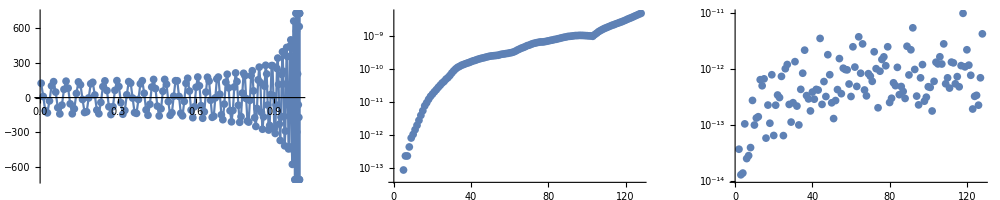

```mathematica
diff[k_,m_,y_]:=2 (k+m) y^(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+m y^(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2];
check[mc,"worland_diff_l",diff];
```

```mathematica
D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{8.88178×10^-16,7.10543×10^-15,1.06581×10^-14,2.84217×10^-14,8.52651×10^-14,1.42109×10^-13,2.13163×10^-13,3.69482×10^-13,4.54747×10^-13,5.68434×10^-13,1.02318×10^-12,1.59162×10^-12,2.16005×10^-12,3.41061×10^-12,4.77485×10^-12,6.82121×10^-12,8.29914×10^-12,1.03455×10^-11,1.27329×10^-11,1.56888×10^-11,1.77351×10^-11,2.13731×10^-11,2.47837×10^-11,2.93312×10^-11,3.41061×10^-11,3.75167×10^-11,4.27463×10^-11,4.63842×10^-11,5.22959×10^-11,6.23004×10^-11,7.18501×10^-11,8.2764×10^-11,9.09495×10^-11,9.82254×10^-11,1.06411×10^-10,1.10958×10^-10,1.17325×10^-10,1.21872×10^-10,1.24601×10^-10,1.29148×10^-10,1.32786×10^-10,1.31877×10^-10,1.30058×10^-10,1.29148×10^-10,1.30967×10^-10,1.45519×10^-10,1.58252×10^-10,1.67347×10^-10,1.87356×10^-10,1.90994×10^-10,2.12822×10^-10,2.20098×10^-10,2.45564×10^-10,2.56478×10^-10,2.72848×10^-10,2.92857×10^-10,3.18323×10^-10,3.4197×10^-10,3.67436×10^-10,3.98359×10^-10,4.311×10^-10,4.62023×10^-10,4.91127×10^-10,5.02041×10^-10,5.20231×10^-10,5.20231×10^-10,5.20231×10^-10,5.20231×10^-10,5.34783×10^-10,5.34783×10^-10,5.42059×10^-10,5.60249×10^-10,5.74801×10^-10,5.89353×10^-10,6.22094×10^-10,6.43922×10^-10,6.98492×10^-10,7.34872×10^-10,7.67614×10^-10,8.11269×10^-10,8.51287×10^-10,8.80391×10^-10,9.16771×10^-10,9.31323×10^-10,9.38599×10^-10,9.34961×10^-10,9.27685×10^-10,9.13133×10^-10,8.91305×10^-10,8.80391×10^-10,8.44011×10^-10,8.51287×10^-10,8.00355×10^-10,7.63976×10^-10,7.31234×10^-10,7.45786×10^-10,7.567×10^-10,7.63976×10^-10,7.67614×10^-10,7.7307×10^-10,7.82165×10^-10,7.82165×10^-10,7.76708×10^-10,7.78527×10^-10,7.82165×10^-10,7.89441×10^-10,7.94898×10^-10,7.93079×10^-10,7.98536×10^-10,8.05812×10^-10,8.13088×10^-10,8.13088×10^-10,8.14907×10^-10,8.18545×10^-10,8.24002×10^-10,9.16771×10^-10,1.05501×10^-9,1.17143×10^-9,1.34605×10^-9,1.50612×10^-9,1.6953×10^-9,1.86992×10^-9,2.0591×10^-9,2.2992×10^-9,2.55386×10^-9,2.8158×10^-9,3.09228×10^-9,3.34694×10^-9}

{6.36447×10^-16,1.05192×10^-14,2.6996×10^-14,1.20316×10^-14,9.52402×10^-15,5.3066×10^-14,4.70389×10^-14,4.366×10^-14,1.0254×10^-12,1.38147×10^-13,1.41207×10^-13,1.14725×10^-13,7.9958×10^-13,3.85015×10^-12,3.83335×10^-12,6.62611×10^-14,1.35044×10^-13,1.17992×10^-12,1.55295×10^-13,4.55593×10^-13,4.33528×10^-14,4.45046×10^-14,2.5516×10^-13,1.74291×10^-13,6.95003×10^-13,5.07735×10^-13,8.26683×10^-13,9.00518×10^-12,6.41334×10^-12,7.25182×10^-13,4.86318×10^-13,3.24262×10^-13,1.37553×10^-13,3.74808×10^-13,3.04118×10^-13,2.63075×10^-12,3.8551×10^-13,3.06387×10^-13,1.91141×10^-12,3.66984×10^-13,2.49816×10^-13,4.54625×10^-12,9.98795×10^-12,4.658×10^-12,3.43858×10^-13,6.07972×10^-13,1.19265×10^-12,4.17115×10^-13,2.50616×10^-12,2.38273×10^-13,1.00113×10^-12,2.35043×10^-13,2.98592×10^-12,8.61945×10^-12,3.55616×10^-13,3.91405×10^-12,3.18182×10^-12,3.11152×10^-13,1.1207×10^-12,2.53409×10^-13,6.29397×10^-13,3.64428×10^-13,3.82864×10^-13,7.28712×10^-13,9.09859×10^-13,1.33035×10^-12,1.21227×10^-12,2.93775×10^-13,4.37694×10^-12,1.06916×10^-12,2.14766×10^-12,2.1087×10^-12,3.97514×10^-13,2.18933×10^-13,4.59601×10^-13,9.36481×10^-13,2.53931×10^-12,5.70284×10^-13,4.89095×10^-12,4.50979×10^-13,3.70386×10^-13,1.36664×10^-12,8.27056×10^-13,1.82369×10^-12,1.38598×10^-11,1.52446×10^-12,1.70016×10^-12,1.63351×10^-12,4.0237×10^-12,4.98686×10^-13,5.90368×10^-12,5.63839×10^-13,9.70668×10^-13,1.44687×10^-12,2.44537×10^-13,5.31446×10^-13,9.22339×10^-13,1.11786×10^-12,1.4768×10^-12,8.6604×10^-13,2.97407×10^-12,4.16324×10^-13,3.99365×10^-13,2.00058×10^-13,4.89086×10^-13,4.272×10^-13,1.57644×10^-12,2.73367×10^-10,9.60285×10^-13,1.50123×10^-12,1.14156×10^-12,3.97868×10^-12,3.29929×10^-12,5.63701×10^-13,5.27306×10^-13,3.24965×10^-13,5.12171×10^-12,3.1571×10^-13,8.99278×10^-13,4.65481×10^-13,5.68262×10^-13,7.62947×10^-13,7.99262×10^-12,1.02135×10^-12,4.98544×10^-13,4.41102×10^-13,7.72565×10^-13,3.84498×10^-12}

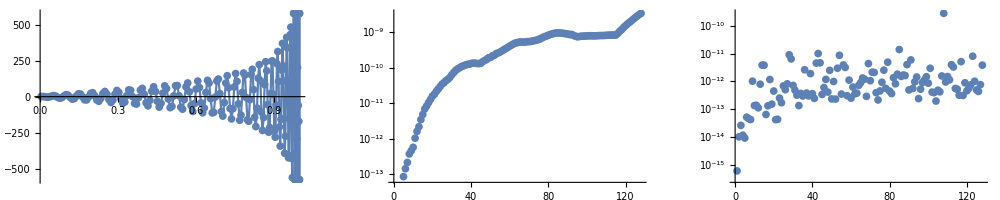

```mathematica
diffr[k_,m_,y_]:=y^m (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
check[mc,"worland_diffr_l",diffr];
```

```mathematica
1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}]//Simplify
```

y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2])

{8.88178×10^-16,5.32907×10^-15,1.06581×10^-14,2.13163×10^-14,9.9476×10^-14,1.98952×10^-13,2.27374×10^-13,4.54747×10^-13,7.95808×10^-13,1.13687×10^-12,1.42109×10^-12,2.04636×10^-12,2.72848×10^-12,3.86535×10^-12,5.34328×10^-12,7.50333×10^-12,9.32232×10^-12,1.18234×10^-11,1.45519×10^-11,1.7053×10^-11,2.02363×10^-11,2.27374×10^-11,2.66027×10^-11,3.20597×10^-11,3.70619×10^-11,4.16094×10^-11,4.82032×10^-11,5.27507×10^-11,6.09361×10^-11,7.41238×10^-11,8.6402×10^-11,9.86802×10^-11,1.10049×10^-10,1.18234×10^-10,1.2642×10^-10,1.33696×10^-10,1.41881×10^-10,1.48248×10^-10,1.54614×10^-10,1.63709×10^-10,1.72804×10^-10,1.8008×10^-10,1.87356×10^-10,1.9736×10^-10,2.05546×10^-10,2.11912×10^-10,2.17369×10^-10,2.27374×10^-10,2.36469×10^-10,2.41926×10^-10,2.43745×10^-10,2.49202×10^-10,2.5284×10^-10,2.58296×10^-10,2.67391×10^-10,2.71029×10^-10,2.76486×10^-10,2.874×10^-10,2.89219×10^-10,3.0559×10^-10,3.09228×10^-10,3.20142×10^-10,3.40151×10^-10,3.72893×10^-10,3.89264×10^-10,4.22006×10^-10,4.42014×10^-10,4.65661×10^-10,4.92946×10^-10,5.20231×10^-10,5.47516×10^-10,5.7662×10^-10,5.98448×10^-10,6.07542×10^-10,6.31189×10^-10,6.38465×10^-10,6.53017×10^-10,6.67569×10^-10,6.78483×10^-10,7.03949×10^-10,7.16682×10^-10,7.40329×10^-10,7.67614×10^-10,7.78527×10^-10,8.13088×10^-10,8.42192×10^-10,8.73115×10^-10,8.94943×10^-10,9.1859×10^-10,9.38599×10^-10,9.65883×10^-10,9.80435×10^-10,9.96806×10^-10,1.00954×10^-9,1.02227×10^-9,1.02773×10^-9,1.02773×10^-9,1.02773×10^-9,1.00954×10^-9,1.00772×10^-9,9.93168×10^-10,9.84073×10^-10,9.65883×10^-10,1.07684×10^-9,1.20053×10^-9,1.32422×10^-9,1.43336×10^-9,1.54978×10^-9,1.62981×10^-9,1.73895×10^-9,1.85537×10^-9,1.94996×10^-9,2.07365×10^-9,2.17551×10^-9,2.29193×10^-9,2.41562×10^-9,2.54659×10^-9,2.65572×10^-9,2.8158×10^-9,2.99042×10^-9,3.17959×10^-9,3.35422×10^-9,3.54339×10^-9,3.76895×10^-9,4.00905×10^-9,4.25644×10^-9,4.51837×10^-9,4.77303×10^-9}

{3.93564×10^-16,1.42291×10^-14,4.73867×10^-15,1.59531×10^-14,2.27971×10^-14,3.11742×10^-14,4.27915×10^-14,3.66123×10^-14,3.59016×10^-13,8.76132×10^-14,1.34331×10^-13,8.59646×10^-14,1.12692×10^-12,6.40481×10^-12,1.03201×10^-11,6.21777×10^-14,1.37751×10^-13,1.1313×10^-12,1.77947×10^-13,1.04642×10^-12,2.50686×10^-13,1.21115×10^-13,1.55733×10^-13,1.59508×10^-13,6.06692×10^-13,2.58504×10^-13,3.9448×10^-13,4.28978×10^-12,2.56113×10^-12,2.54925×10^-13,4.77212×10^-13,3.23321×10^-13,1.00948×10^-13,2.89837×10^-13,2.71773×10^-13,2.31812×10^-12,3.35159×10^-13,2.82562×10^-13,8.82064×10^-13,7.9857×10^-13,3.30345×10^-13,6.64872×10^-12,3.80418×10^-12,3.97864×10^-12,4.0487×10^-13,7.62143×10^-13,3.2433×10^-13,2.79942×10^-12,2.52998×10^-12,2.81935×10^-13,6.23607×10^-13,1.41473×10^-13,2.68838×10^-12,8.41218×10^-12,3.66304×10^-13,2.68838×10^-12,2.72772×10^-12,5.82884×10^-13,1.31525×10^-12,4.30098×10^-13,6.76342×10^-13,7.69588×10^-13,3.15196×10^-13,6.65526×10^-13,2.31344×10^-12,3.63769×10^-13,1.29468×10^-12,2.83672×10^-13,4.11526×10^-12,4.2408×10^-13,3.28046×10^-12,2.02577×10^-12,3.76204×10^-13,2.04036×10^-13,4.29654×10^-13,1.7533×10^-13,2.11476×10^-12,3.05021×10^-13,2.44867×10^-12,2.25554×10^-13,1.99385×10^-13,1.66365×10^-12,5.72815×10^-13,9.38869×10^-13,7.10255×10^-12,7.7979×10^-13,1.1807×10^-12,2.86805×10^-12,3.13492×10^-12,5.22115×10^-13,2.12232×10^-11,3.36955×10^-13,9.86724×10^-13,6.80122×10^-13,2.36898×10^-13,7.36079×10^-13,9.0156×10^-13,9.238×10^-13,1.23158×10^-12,8.11902×10^-13,1.03354×10^-12,3.48572×10^-13,5.02726×10^-13,3.16575×10^-13,1.34433×10^-12,3.59084×10^-13,1.24813×10^-12,2.75655×10^-10,8.78908×10^-13,1.43609×10^-12,4.60564×10^-13,3.29564×10^-12,3.4684×10^-12,4.19258×10^-13,5.26669×10^-13,1.67699×10^-13,4.73466×10^-12,2.62862×10^-13,5.79416×10^-13,7.01979×10^-13,1.20655×10^-12,1.04047×10^-12,9.33266×10^-12,1.15803×10^-12,5.47777×10^-13,3.84924×10^-13,6.75683×10^-13,3.48584×10^-12}

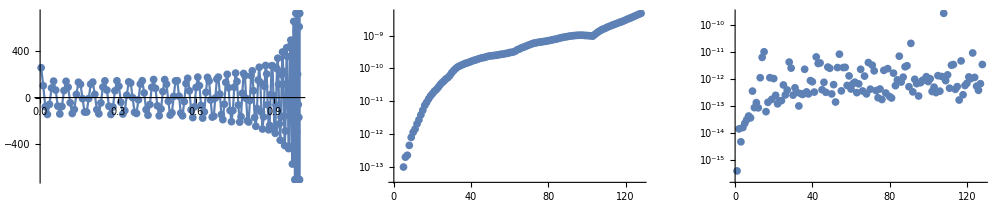

```mathematica
divrdiffr[k_,m_,y_]:=y^(-1+m) (2 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]);
check[mc,"worland_divrdiffr_l",divrdiffr];
```

```mathematica
D[1/y D[y y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],y]//Simplify
```

y^(-2+m) (4 (k+k^2+m+2 k m+m^2) y^4 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) (4 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]))

{2.5818×10^-11,1.42109×10^-14,1.42109×10^-13,6.82121×10^-13,2.27374×10^-12,6.36646×10^-12,2.00089×10^-11,4.00178×10^-11,4.72937×10^-11,8.73115×10^-11,1.30967×10^-10,2.47383×10^-10,3.20142×10^-10,4.65661×10^-10,7.27596×10^-10,1.04774×10^-9,1.22236×10^-9,1.86265×10^-9,3.0268×10^-9,3.95812×10^-9,4.65661×10^-9,7.21775×10^-9,9.31323×10^-9,1.30385×10^-8,1.67638×10^-8,2.09548×10^-8,2.65427×10^-8,3.07336×10^-8,3.53903×10^-8,4.09782×10^-8,4.93601×10^-8,5.86733×10^-8,6.42613×10^-8,7.26432×10^-8,8.47504×10^-8,9.31323×10^-8,9.87202×10^-8,1.08033×10^-7,1.17347×10^-7,1.23866×10^-7,1.43424×10^-7,1.6205×10^-7,1.9744×10^-7,2.19792×10^-7,2.5332×10^-7,2.83122×10^-7,3.1665×10^-7,3.42727×10^-7,3.53903×10^-7,3.8743×10^-7,4.02331×10^-7,4.47035×10^-7,5.1409×10^-7,5.81145×10^-7,6.55651×10^-7,7.37607×10^-7,8.04663×10^-7,8.86619×10^-7,9.83477×10^-7,1.05798×10^-6,1.13249×10^-6,1.14739×10^-6,1.19209×10^-6,1.2964×10^-6,1.38581×10^-6,1.51992×10^-6,1.68383×10^-6,1.96695×10^-6,2.05636×10^-6,2.32458×10^-6,2.38419×10^-6,2.5928×10^-6,2.83122×10^-6,3.06964×10^-6,3.30806×10^-6,3.51667×10^-6,3.8445×10^-6,4.14252×10^-6,4.47035×10^-6,4.82798×10^-6,5.06639×10^-6,5.33462×10^-6,5.60284×10^-6,5.72205×10^-6,5.84126×10^-6,6.02007×10^-6,6.31809×10^-6,6.31809×10^-6,6.49691×10^-6,6.61612×10^-6,6.3777×10^-6,6.25849×10^-6,6.25849×10^-6,6.25849×10^-6,6.02007×10^-6,6.07967×10^-6,6.3777×10^-6,6.73532×10^-6,6.97374×10^-6,7.15256×10^-6,7.7486×10^-6,8.28505×10^-6,8.82149×10^-6,9.11951×10^-6,9.71556×10^-6,0.000010252,0.0000106692,0.0000110865,0.0000116825,0.0000122786,0.0000129342,0.0000136495,0.0000143051,0.0000149012,0.0000154972,0.0000159144,0.0000161529,0.0000163317,0.0000168085,0.0000168085,0.0000171065,0.000017643,0.000017941,0.000018239,0.0000181794,0.0000184774,0.0000185966,0.0000186563}

{1.,6.82401×10^-16,4.94327×10^-14,5.37923×10^-13,3.14063×10^-14,5.93518×10^-14,6.1488×10^-14,6.85018×10^-14,5.13081×10^-14,8.14689×10^-14,5.30493×10^-14,5.35467×10^-12,7.18648×10^-14,3.65365×10^-13,5.17227×10^-14,7.85341×10^-14,7.22585×10^-14,2.61239×10^-13,2.92752×10^-12,2.43339×10^-13,5.95577×10^-12,5.76689×10^-14,2.8015×10^-13,1.4342×10^-12,2.18972×10^-13,1.11582×10^-13,2.18324×10^-13,1.03721×10^-13,3.73996×10^-13,5.72121×10^-12,1.19709×10^-11,1.33134×10^-13,7.18497×10^-13,1.89512×10^-13,2.16331×10^-13,1.27421×10^-13,1.40303×10^-13,6.85225×10^-13,6.84142×10^-13,4.93217×10^-14,3.19474×10^-13,8.21639×10^-14,2.12914×10^-13,3.45488×10^-13,1.47356×10^-12,8.12755×10^-13,5.97766×10^-13,1.54677×10^-12,5.06992×10^-13,9.36176×10^-13,8.35165×10^-13,7.07084×10^-13,2.35533×10^-13,6.61923×10^-13,5.19538×10^-13,4.44707×10^-13,7.01934×10^-13,4.90543×10^-13,3.5747×10^-12,2.59412×10^-13,1.56454×10^-12,5.58508×10^-13,2.05494×10^-12,1.84827×10^-12,3.87702×10^-13,1.08515×10^-13,3.62186×10^-13,8.4802×10^-13,5.42011×10^-13,2.79192×10^-13,2.02114×10^-12,4.26692×10^-12,1.68505×10^-13,1.58709×10^-13,1.76098×10^-13,1.98096×10^-13,5.57983×10^-13,6.66474×10^-13,3.03799×10^-10,5.36652×10^-13,5.81404×10^-13,1.78633×10^-12,8.04091×10^-13,3.14926×10^-12,4.21691×10^-12,4.12472×10^-12,1.84385×10^-12,3.34844×10^-12,9.52143×10^-13,1.89546×10^-12,2.20733×10^-12,1.54651×10^-12,9.78873×10^-13,6.17218×10^-13,2.63451×10^-13,1.02928×10^-12,1.18433×10^-11,2.38193×10^-13,2.76181×10^-13,1.30577×10^-11,4.65145×10^-13,3.61681×10^-13,2.39388×10^-12,2.4487×10^-11,4.72785×10^-13,2.33073×10^-12,4.49702×10^-12,1.78511×10^-12,3.94183×10^-12,4.50918×10^-13,1.0826×10^-12,4.24368×10^-12,1.93388×10^-11,9.52882×10^-13,5.61127×10^-13,2.09341×10^-11,4.06277×10^-13,5.37053×10^-13,2.22741×10^-13,1.58158×10^-12,1.73894×10^-13,5.12639×10^-12,3.95403×10^-13,2.50741×10^-12,5.8357×10^-13,5.87134×10^-13,1.71819×10^-12,3.53273×10^-13}

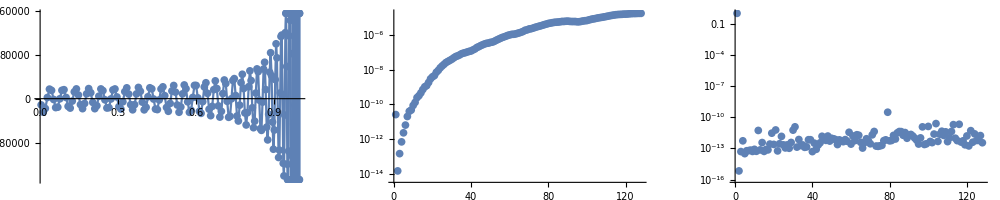

```mathematica
diffdivrdiffr[k_,m_,y_]:=y^(-2+m) (4 (k+k^2+m+2 k m+m^2) y^4 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) (4 (k+m) y^2 JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]+(-1+m) JacobiP[k,-1/2,-1/2+m,-1+2 y^2]));
check[mc,"worland_diffdivrdiffr_l",diffdivrdiffr];
```

```mathematica
1/y^2 D[y^2 D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m(m+1)y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

```mathematica
slapl[0,5,0]//Simplify
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

{2.5818×10^-11,1.42109×10^-14,1.13687×10^-13,6.82121×10^-13,2.72848×10^-12,6.36646×10^-12,1.45519×10^-11,3.27418×10^-11,5.09317×10^-11,7.27596×10^-11,1.30967×10^-10,2.03727×10^-10,2.91038×10^-10,4.94765×10^-10,7.85803×10^-10,1.04774×10^-9,1.33878×10^-9,1.86265×10^-9,2.79397×10^-9,3.84171×10^-9,5.47152×10^-9,6.98492×10^-9,1.04774×10^-8,1.234×10^-8,1.53668×10^-8,2.04891×10^-8,2.65427×10^-8,3.0268×10^-8,3.53903×10^-8,4.00469×10^-8,4.84288×10^-8,5.7742×10^-8,6.42613×10^-8,7.17118×10^-8,8.3819×10^-8,9.31323×10^-8,9.68575×10^-8,1.04308×10^-7,1.11759×10^-7,1.2666×10^-7,1.44355×10^-7,1.6205×10^-7,1.9744×10^-7,2.16067×10^-7,2.49594×10^-7,2.83122×10^-7,3.09199×10^-7,3.31551×10^-7,3.57628×10^-7,3.7998×10^-7,4.02331×10^-7,4.39584×10^-7,5.06639×10^-7,5.81145×10^-7,6.55651×10^-7,7.45058×10^-7,8.12113×10^-7,8.79169×10^-7,9.68575×10^-7,1.05798×10^-6,1.11759×10^-6,1.16229×10^-6,1.20699×10^-6,1.2815×10^-6,1.38581×10^-6,1.50502×10^-6,1.75834×10^-6,1.93715×10^-6,2.08616×10^-6,2.26498×10^-6,2.44379×10^-6,2.563×10^-6,2.86102×10^-6,3.06964×10^-6,3.27826×10^-6,3.66569×10^-6,3.8147×10^-6,4.20213×10^-6,4.55976×10^-6,4.82798×10^-6,5.06639×10^-6,5.24521×10^-6,5.57303×10^-6,5.72205×10^-6,5.78165×10^-6,6.07967×10^-6,6.31809×10^-6,6.31809×10^-6,6.55651×10^-6,6.61612×10^-6,6.49691×10^-6,6.25849×10^-6,6.19888×10^-6,6.19888×10^-6,5.96046×10^-6,5.90086×10^-6,6.31809×10^-6,6.55651×10^-6,6.67572×10^-6,7.09295×10^-6,7.7486×10^-6,8.22544×10^-6,8.64267×10^-6,9.23872×10^-6,9.53674×10^-6,0.0000101328,0.0000107288,0.0000110269,0.0000116229,0.0000121593,0.0000128746,0.000013411,0.0000141263,0.000014782,0.0000155568,0.0000158548,0.0000160336,0.0000162721,0.0000167489,0.0000168085,0.0000171065,0.0000174642,0.0000178218,0.0000180602,0.0000181794,0.0000182986,0.0000185966,0.0000186563}

{1.,5.88703×10^-16,2.73283×10^-14,6.4625×10^-13,2.3062×10^-14,4.14225×10^-14,2.38848×10^-13,2.07685×10^-14,1.08734×10^-12,1.09077×10^-13,1.39539×10^-13,1.87697×10^-12,3.63066×10^-14,3.67156×10^-13,3.27418×10^-13,3.06024×10^-13,2.50696×10^-13,2.22608×10^-12,8.04695×10^-14,4.77218×10^-12,4.30544×10^-13,4.32981×10^-13,6.23455×10^-14,6.9892×10^-13,2.02997×10^-13,3.49439×10^-13,3.85455×10^-13,1.40576×10^-13,7.08145×10^-14,4.23056×10^-12,1.38445×10^-13,1.5325×10^-13,3.86376×10^-13,4.62272×10^-13,7.53719×10^-12,3.26165×10^-13,1.14783×10^-13,9.82199×10^-13,7.78058×10^-13,2.17487×10^-13,6.10128×10^-13,6.70429×10^-13,2.13443×10^-13,3.41181×10^-13,1.21343×10^-13,2.14635×10^-13,3.2131×10^-13,2.23494×10^-13,2.91887×10^-12,1.19612×10^-12,8.44393×10^-13,7.00838×10^-13,3.41175×10^-13,1.86948×10^-13,4.91242×10^-13,5.97831×10^-13,5.539×10^-13,1.075×10^-13,5.19923×10^-13,1.7324×10^-13,1.98922×10^-12,5.60703×10^-13,2.01495×10^-12,7.97625×10^-12,1.58095×10^-12,5.30082×10^-13,3.20781×10^-13,5.65021×10^-12,5.21947×10^-13,1.53121×10^-13,7.40907×10^-13,1.36904×10^-12,3.42893×10^-13,1.2742×10^-13,1.08239×10^-11,4.6733×10^-13,4.42778×10^-13,4.21125×10^-12,1.66188×10^-12,5.58024×10^-13,5.76542×10^-13,2.03498×10^-12,2.46935×10^-13,2.75933×10^-12,5.93843×10^-13,4.48194×10^-13,4.01938×10^-12,3.42405×10^-12,1.73424×10^-12,1.73373×10^-11,2.23418×10^-12,1.07208×10^-12,7.14934×10^-13,1.0307×10^-12,4.40936×10^-13,5.1762×10^-13,1.59027×10^-12,2.93511×10^-13,2.67645×10^-13,6.45997×10^-13,5.032×10^-13,3.26497×10^-12,3.6139×10^-13,1.64049×10^-12,4.79407×10^-13,8.56612×10^-12,2.15332×10^-12,1.77469×10^-12,1.55399×10^-12,1.67228×10^-12,1.97788×10^-12,1.97356×10^-12,3.4602×10^-12,9.51451×10^-13,5.07206×10^-11,2.66812×10^-12,2.06587×10^-12,6.65855×10^-13,2.32806×10^-13,7.87577×10^-12,1.74133×10^-13,2.63289×10^-12,3.96588×10^-13,2.53519×10^-12,4.28985×10^-12,9.4047×10^-13,2.92968×10^-12,5.42861×10^-13}

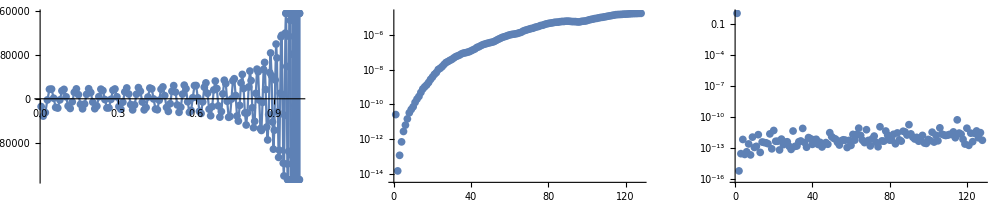

```mathematica
slapl[k_,m_,y_]:=2 (k+m) y^m (2 (1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(3+2 m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[mc,"worland_slapl_l",slapl];
```

```mathematica
1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2//Simplify
```

4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{2.5818×10^-11,7.10543×10^-15,1.42109×10^-13,6.82121×10^-13,2.27374×10^-12,6.36646×10^-12,1.81899×10^-11,3.63798×10^-11,5.09317×10^-11,8.00355×10^-11,1.30967×10^-10,2.18279×10^-10,3.20142×10^-10,4.94765×10^-10,7.85803×10^-10,1.04774×10^-9,1.33878×10^-9,1.97906×10^-9,2.91038×10^-9,3.60887×10^-9,4.5402×10^-9,6.75209×10^-9,9.31323×10^-9,1.28057×10^-8,1.58325×10^-8,2.04891×10^-8,2.65427×10^-8,3.07336×10^-8,3.49246×10^-8,4.19095×10^-8,4.74975×10^-8,5.86733×10^-8,6.70552×10^-8,7.54371×10^-8,8.28877×10^-8,9.12696×10^-8,9.68575×10^-8,1.06171×10^-7,1.17347×10^-7,1.23866×10^-7,1.45286×10^-7,1.60187×10^-7,1.93715×10^-7,2.12342×10^-7,2.5332×10^-7,2.83122×10^-7,3.09199×10^-7,3.46452×10^-7,3.53903×10^-7,3.8743×10^-7,4.09782×10^-7,4.47035×10^-7,5.06639×10^-7,5.81145×10^-7,6.55651×10^-7,7.22706×10^-7,8.04663×10^-7,8.9407×10^-7,9.83477×10^-7,1.07288×10^-6,1.11759×10^-6,1.16229×10^-6,1.19209×10^-6,1.2666×10^-6,1.40071×10^-6,1.51992×10^-6,1.68383×10^-6,1.96695×10^-6,2.05636×10^-6,2.29478×10^-6,2.38419×10^-6,2.563×10^-6,2.77162×10^-6,3.06964×10^-6,3.30806×10^-6,3.51667×10^-6,3.8445×10^-6,4.14252×10^-6,4.47035×10^-6,4.76837×10^-6,5.03659×10^-6,5.33462×10^-6,5.54323×10^-6,5.72205×10^-6,5.78165×10^-6,6.02007×10^-6,6.31809×10^-6,6.19888×10^-6,6.49691×10^-6,6.49691×10^-6,6.55651×10^-6,6.25849×10^-6,6.25849×10^-6,6.25849×10^-6,5.90086×10^-6,6.07967×10^-6,6.31809×10^-6,6.67572×10^-6,6.91414×10^-6,7.09295×10^-6,7.689×10^-6,8.22544×10^-6,8.76188×10^-6,9.11951×10^-6,9.65595×10^-6,0.0000101328,0.0000106096,0.0000110865,0.0000116825,0.000012219,0.0000128746,0.000013411,0.0000142455,0.0000148416,0.0000154376,0.0000158548,0.0000160933,0.0000163317,0.0000167489,0.0000168681,0.0000171065,0.000017643,0.000017941,0.0000181198,0.0000181794,0.0000184178,0.000018537,0.0000185966}

{1.,6.82401×10^-16,9.44899×10^-14,5.86864×10^-13,3.12822×10^-14,7.25885×10^-14,6.10274×10^-14,6.97186×10^-14,4.78186×10^-14,8.84757×10^-14,5.28542×10^-14,5.29149×10^-12,6.97287×10^-14,3.57255×10^-13,5.59303×10^-14,7.85341×10^-14,7.16954×10^-14,2.60554×10^-13,2.94528×10^-12,2.41617×10^-13,5.8852×10^-12,5.78763×10^-14,2.76165×10^-13,1.43394×10^-12,2.19094×10^-13,1.12803×10^-13,2.19237×10^-13,1.03319×10^-13,3.735×10^-13,5.71934×10^-12,1.1963×10^-11,1.32524×10^-13,7.21099×10^-13,1.90079×10^-13,2.1464×10^-13,1.27244×10^-13,1.40303×10^-13,6.85085×10^-13,6.84142×10^-13,4.93217×10^-14,3.21845×10^-13,8.21639×10^-14,2.1309×10^-13,3.45851×10^-13,1.48895×10^-12,8.11936×10^-13,5.97205×10^-13,1.54378×10^-12,5.0648×10^-13,9.3632×10^-13,8.35287×10^-13,7.07084×10^-13,2.35533×10^-13,6.83331×10^-13,5.19367×10^-13,4.40925×10^-13,7.0227×10^-13,4.90735×10^-13,3.57977×10^-12,2.59587×10^-13,1.56713×10^-12,5.58508×10^-13,2.05494×10^-12,1.85346×10^-12,3.87312×10^-13,1.08515×10^-13,3.67234×10^-13,8.48451×10^-13,5.51302×10^-13,2.82501×10^-13,2.0157×10^-12,4.268×10^-12,1.68505×10^-13,1.59251×10^-13,1.7653×10^-13,1.98251×10^-13,5.5764×10^-13,6.6664×10^-13,3.03747×10^-10,5.36484×10^-13,5.81122×10^-13,1.78709×10^-12,8.06064×10^-13,3.14755×10^-12,4.22605×10^-12,4.12316×10^-12,1.84364×10^-12,3.34844×10^-12,9.51754×10^-13,1.89835×10^-12,2.20383×10^-12,1.55786×10^-12,9.80338×10^-13,6.16999×10^-13,2.63451×10^-13,1.03317×10^-12,1.18444×10^-11,2.37808×10^-13,2.77198×10^-13,1.30571×10^-11,4.65145×10^-13,3.61681×10^-13,2.39719×10^-12,2.44737×10^-11,4.72591×10^-13,2.33133×10^-12,4.49657×10^-12,1.78511×10^-12,3.94354×10^-12,4.50515×10^-13,1.08281×10^-12,4.28121×10^-12,1.9335×10^-11,9.53002×10^-13,5.61264×10^-13,2.09285×10^-11,4.06277×10^-13,5.37053×10^-13,2.22741×10^-13,1.58324×10^-12,1.74036×10^-13,5.12656×10^-12,3.95531×10^-13,2.5076×10^-12,5.83389×10^-13,5.86935×10^-13,1.7183×10^-12,3.53143×10^-13}

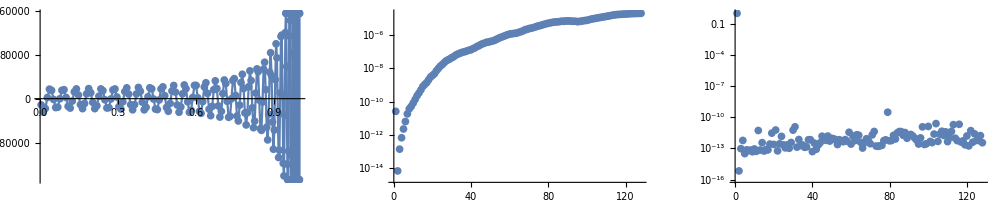

```mathematica
claplh[k_,m_,y_]:=4 (k+m) y^m ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[mc,"worland_claplh_l",claplh];
```

```mathematica
1/y^2 D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^3//Simplify
```

4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{6.44303×10^-9,0.,1.42109×10^-13,6.82121×10^-13,2.27374×10^-12,5.45697×10^-12,1.45519×10^-11,2.72848×10^-11,4.54747×10^-11,8.00355×10^-11,1.60071×10^-10,2.61934×10^-10,3.7835×10^-10,5.82077×10^-10,8.44011×10^-10,1.22236×10^-9,1.62981×10^-9,2.32831×10^-9,3.25963×10^-9,4.19095×10^-9,5.58794×10^-9,7.21775×10^-9,1.07102×10^-8,1.234×10^-8,1.55997×10^-8,2.00234×10^-8,2.37487×10^-8,2.84053×10^-8,3.07336×10^-8,3.81842×10^-8,4.37722×10^-8,5.30854×10^-8,5.7742×10^-8,6.42613×10^-8,7.45058×10^-8,8.9407×10^-8,1.05239×10^-7,1.22003×10^-7,1.38767×10^-7,1.55531×10^-7,1.72295×10^-7,1.86265×10^-7,2.10479×10^-7,2.30968×10^-7,2.48663×10^-7,2.66358×10^-7,2.84053×10^-7,3.0268×10^-7,3.1665×10^-7,3.29688×10^-7,3.40864×10^-7,3.50177×10^-7,3.61353×10^-7,3.83705×10^-7,4.17233×10^-7,4.58211×10^-7,5.06639×10^-7,5.62519×10^-7,6.10948×10^-7,6.55651×10^-7,7.0408×10^-7,7.33882×10^-7,7.71135×10^-7,8.15839×10^-7,8.49366×10^-7,8.97795×10^-7,9.42498×10^-7,1.0021×10^-6,1.03563×10^-6,1.08965×10^-6,1.13063×10^-6,1.16415×10^-6,1.20699×10^-6,1.3113×10^-6,1.46031×10^-6,1.63913×10^-6,1.78814×10^-6,2.05636×10^-6,2.20537×10^-6,2.44379×10^-6,2.6226×10^-6,2.80142×10^-6,3.09944×10^-6,3.09944×10^-6,3.27826×10^-6,3.66569×10^-6,4.26173×10^-6,4.67896×10^-6,5.39422×10^-6,5.87106×10^-6,6.52671×10^-6,6.97374×10^-6,7.53999×10^-6,7.98702×10^-6,8.52346×10^-6,8.76188×10^-6,9.17912×10^-6,9.47714×10^-6,9.59635×10^-6,9.89437×10^-6,0.00001055,0.0000110865,0.0000116825,0.0000120997,0.000012517,0.0000132918,0.0000138879,0.0000143051,0.0000149012,0.0000156164,0.0000163913,0.0000174046,0.0000181794,0.0000191927,0.0000201464,0.0000209808,0.0000219345,0.0000226498,0.000023663,0.0000243783,0.0000251532,0.0000259876,0.0000270009,0.0000277758,0.0000283122,0.0000290871,0.0000299215,0.0000302792}

{1.,0.,1.33217×10^-13,5.25253×10^-13,3.34643×10^-14,7.00228×10^-14,2.23309×10^-14,2.66094×10^-14,2.79892×10^-14,6.0489×10^-14,7.03897×10^-14,5.03301×10^-12,1.04192×10^-13,2.26633×10^-13,1.2442×10^-13,1.10045×10^-13,1.04003×10^-13,1.99206×10^-13,3.7727×10^-12,1.51437×10^-12,7.54576×10^-12,6.08349×10^-14,4.06251×10^-13,4.19883×10^-13,1.47021×10^-13,1.47542×10^-13,3.54216×10^-13,9.14383×10^-14,4.40572×10^-13,2.56493×10^-13,1.16266×10^-11,1.79322×10^-13,1.05699×10^-12,2.59283×10^-13,1.25526×10^-13,7.83797×10^-14,1.1312×10^-13,2.47872×10^-13,5.458×10^-13,4.33515×10^-14,2.01394×10^-13,1.13852×10^-13,1.48842×10^-13,1.91086×10^-13,1.16556×10^-12,7.38032×10^-13,6.81073×10^-13,1.79358×10^-12,5.67194×10^-13,9.85058×10^-13,5.52169×10^-13,4.63727×10^-13,1.52913×10^-13,1.87166×10^-12,4.30465×10^-13,2.02548×10^-13,8.00605×10^-13,5.7766×10^-13,3.87286×10^-12,4.82567×10^-13,2.94102×10^-12,8.14584×10^-13,1.60745×10^-12,2.49707×10^-12,2.87036×10^-13,1.54584×10^-13,1.31208×10^-13,8.30582×10^-13,5.84135×10^-13,1.3429×10^-13,9.23388×10^-13,5.90475×10^-12,3.28632×10^-13,2.63456×10^-13,2.08024×10^-13,2.00138×10^-13,6.29749×10^-13,7.33188×10^-13,1.05831×10^-10,1.24364×10^-12,1.81076×10^-12,2.13818×10^-12,5.2072×10^-13,2.99797×10^-12,2.76295×10^-12,2.71176×10^-12,9.89164×10^-13,1.83322×10^-12,9.26916×10^-13,2.50893×10^-12,1.62351×10^-12,2.41806×10^-13,7.18151×10^-13,2.78449×10^-13,2.30979×10^-13,7.2986×10^-13,1.95726×10^-11,1.56859×10^-13,1.50403×10^-13,1.31223×10^-11,7.93885×10^-13,4.09996×10^-13,2.29003×10^-12,2.36628×10^-11,6.80221×10^-13,3.65145×10^-12,4.73658×10^-12,1.26548×10^-12,3.5678×10^-12,5.25227×10^-13,3.66273×10^-12,5.70609×10^-12,1.93039×10^-11,1.08012×10^-12,9.09645×10^-13,7.43416×10^-13,3.84249×10^-13,1.13354×10^-12,2.44124×10^-13,1.70047×10^-12,1.8804×10^-13,5.74336×10^-12,2.05896×10^-13,1.29718×10^-12,3.35826×10^-13,4.26788×10^-13,1.61757×10^-12,6.85818×10^-13}

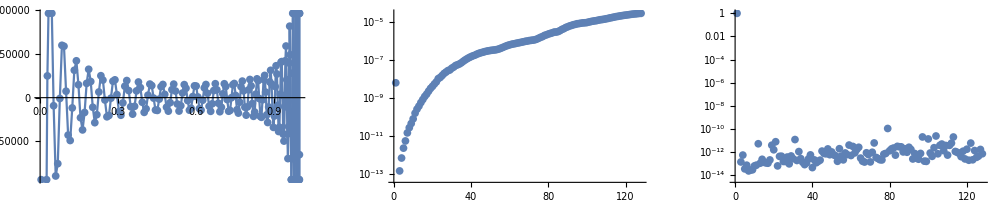

```mathematica
r1claplh[k_,m_,y_]:=4 (k+m) y^(-1+m) ((1+k+m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+(1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[mc,"worland_r_1claplh_l",r1claplh];
```

```mathematica
D[1/y D[y D[ y^m JacobiP[k,-1/2,m-1/2,2 y^2-1],{y,1}],{y,1}]-(m^2 y^m JacobiP[k,-1/2,m-1/2,2 y^2-1])/y^2,{y,1}]//Simplify
```

4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2])

{1.9329×10^-8,3.22155×10^-8,9.09495×10^-13,9.09495×10^-12,5.09317×10^-11,2.18279×10^-10,5.23869×10^-10,1.16415×10^-9,2.79397×10^-9,6.0536×10^-9,1.11759×10^-8,2.6077×10^-8,4.09782×10^-8,7.07805×10^-8,1.11759×10^-7,1.86265×10^-7,2.38419×10^-7,3.72529×10^-7,5.96046×10^-7,9.53674×10^-7,1.3113×10^-6,1.84774×10^-6,2.38419×10^-6,2.74181×10^-6,3.45707×10^-6,4.05312×10^-6,5.48363×10^-6,6.4373×10^-6,8.10623×10^-6,0.0000100136,0.0000114441,0.0000171661,0.0000209808,0.0000257492,0.0000324249,0.000038147,0.0000514984,0.0000591278,0.0000858307,0.0000934601,0.00012207,0.000141144,0.000183105,0.000190735,0.000217438,0.000240326,0.000289917,0.000335693,0.00038147,0.000411987,0.000488281,0.000526428,0.00062561,0.000671387,0.000778198,0.00087738,0.00102234,0.00117493,0.00131989,0.00150299,0.00170135,0.00187683,0.0020752,0.00228882,0.00247955,0.00269318,0.00289154,0.00314331,0.00338745,0.00361633,0.00384521,0.00406647,0.00427246,0.00447464,0.00500488,0.00604248,0.00665283,0.00762939,0.00872803,0.0101318,0.0112305,0.0128174,0.0142822,0.0158691,0.017334,0.0189209,0.0203857,0.0214844,0.0239258,0.0263672,0.0292969,0.03125,0.0341797,0.0380859,0.0395508,0.0419922,0.0419922,0.043457,0.046875,0.0478516,0.0488281,0.046875,0.0488281,0.0488281,0.050293,0.0539551,0.0561523,0.0595703,0.0622559,0.0649414,0.0673828,0.0722656,0.0800781,0.0849609,0.0947266,0.105469,0.115234,0.131836,0.147461,0.160156,0.175781,0.191406,0.208984,0.229492,0.246094,0.271484,0.294922,0.316406}

{1.,8.92196×10^-10,4.78058×10^-14,6.14715×10^-14,1.95887×10^-14,1.28083×10^-13,7.66715×10^-14,1.12611×10^-14,4.09443×10^-14,4.51944×10^-14,3.44634×10^-14,4.18315×10^-13,2.4823×10^-12,1.75764×10^-13,1.27818×10^-13,5.74495×10^-14,3.55561×10^-13,3.33658×10^-13,7.52284×10^-11,6.50808×10^-13,3.16213×10^-13,7.02709×10^-14,1.99237×10^-13,2.29525×10^-13,6.56425×10^-13,2.26225×10^-12,3.08508×10^-12,9.76299×10^-13,2.67035×10^-13,1.40959×10^-13,9.82621×10^-13,9.49308×10^-14,1.27464×10^-13,2.36237×10^-13,1.67911×10^-13,9.19016×10^-13,1.13895×10^-13,3.69032×10^-12,7.19451×10^-14,7.99281×10^-13,8.14566×10^-13,1.2254×10^-11,3.36116×10^-13,2.10111×10^-13,4.7716×10^-13,6.75175×10^-13,3.82669×10^-13,6.0509×10^-13,9.58285×10^-13,4.56138×10^-12,6.49338×10^-14,1.14928×10^-13,9.8582×10^-13,1.37366×10^-12,4.10905×10^-13,4.20308×10^-12,3.5059×10^-13,3.32663×10^-13,5.74344×10^-13,1.04598×10^-13,3.7752×10^-13,4.57491×10^-12,3.88425×10^-13,5.25237×10^-13,1.37591×10^-13,2.36948×10^-12,5.67988×10^-12,2.21275×10^-12,1.33862×10^-12,1.31384×10^-11,3.51557×10^-13,5.55397×10^-13,1.36539×10^-13,1.36622×10^-13,4.04837×10^-13,3.66926×10^-13,6.6672×10^-12,3.43029×10^-13,5.74438×10^-13,1.94075×10^-12,1.28611×10^-12,4.63871×10^-13,4.67077×10^-13,3.75529×10^-13,3.1782×10^-13,3.84477×10^-13,1.10134×10^-12,1.43373×10^-12,4.38336×10^-13,3.69029×10^-13,1.00056×10^-12,7.04763×10^-13,4.07953×10^-13,1.8667×10^-11,1.50467×10^-12,8.9956×10^-13,6.65215×10^-13,3.6981×10^-12,1.11133×10^-12,1.01539×10^-12,4.87759×10^-12,1.09307×10^-12,6.48531×10^-12,1.57068×10^-12,6.89173×10^-13,4.44677×10^-13,4.27533×10^-12,7.03672×10^-12,1.27761×10^-12,2.402×10^-12,1.71625×10^-11,6.41693×10^-13,4.75023×10^-12,6.70645×10^-13,3.35505×10^-12,5.45149×10^-13,1.98991×10^-11,5.57913×10^-13,8.41521×10^-13,1.05986×10^-12,1.8393×10^-12,6.68124×10^-12,4.14647×10^-12,1.59396×10^-12,9.95601×10^-13,1.65125×10^-12,2.40143×10^-12,1.75981×10^-12}

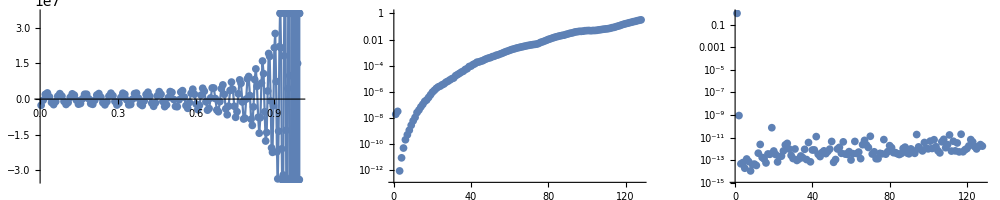

```mathematica
dclaplh[k_,m_,y_]:=4 (k+m) y^(-1+m) (2 (2+k^2+3 m+m^2+k (3+2 m)) y^4 JacobiP[-3+k,5/2,5/2+m,-1+2 y^2]+(1+k+m) (4+3 m) y^2 JacobiP[-2+k,3/2,3/2+m,-1+2 y^2]+m (1+m) JacobiP[-1+k,1/2,1/2+m,-1+2 y^2]);
check[mc,"worland_dclaplh_l",dclaplh];
```

```mathematica
endpoint[mm_,f_,col_]:=Module[{tmp,t,m,norm,data,nn},norm[n_,l_] := Table[√Integrate[((r^l JacobiP[i,-1/2,l-1/2,2 r^2-1])^2)/(√(1-r^2)),{r,0,1}],{i,0,n}];
For[m=0,m≤ mm,m++,
data = Import["cylinder_worland_endpoints_l"<>ToString[m]<>".dat"];
nn=Dimensions[data][[1]]-1;
tmp = norm[nn,m];
t=Table[f[i,1,m]/tmp[[i+1]],{i,0,nn}];
Print[Abs[N[t-data[[;;,col]],16]]];
];
];
```

```mathematica
value[n_,r_,l_]:=r^l JacobiP[n,-1/2,l-1/2,2 r^2-1]
endpoint[3,value,1];
```

{5.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,4.6×10^-16}

{2.1×10^-16,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17,1.×10^-17}

{1.5×10^-16,8.×10^-17,8.×10^-17,6.×10^-17,2.5×10^-16,1.6×10^-16}

{1.3×10^-16,2.×10^-16,8.×10^-17,2.8×10^-16,6.1×10^-16,2.8×10^-16}

```mathematica
diff[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y]/.{y->r}
endpoint[3,diff,2];
```

{0.,6.×10^-17,2.×10^-16,5.×10^-15,1.×10^-15,4.9×10^-14}

{2.1×10^-16,5.×10^-16,2.1×10^-15,7.2×10^-15,6.×10^-16,3.×10^-15}

{3.×10^-16,2.4×10^-15,4.×10^-16,7.1×10^-15,2.8×10^-14,2.2×10^-14}

{6.1×10^-16,3.9×10^-15,3.1×10^-15,1.29×10^-14,7.2×10^-14,3.7×10^-14}

```mathematica
diff2[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,2}]/.{y->r}
endpoint[3,diff2,3];
```

{0.,6.×10^-17,9.4×10^-15,5.4×10^-14,4.×10^-14,1.48×10^-12}

{0.,1.4×10^-15,1.7×10^-14,1.15×10^-13,2.×10^-14,3.5×10^-13}

{3.×10^-16,6.1×10^-15,3.4×10^-14,9.×10^-14,1.01×10^-12,7.9×10^-13}

{1.23×10^-15,2.4×10^-14,2.7×10^-14,2.8×10^-13,2.65×10^-12,1.5×10^-12}

```mathematica
diff3[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,3}]/.{y->r}
endpoint[3,diff3,4];
```

{0.,0.,1.1×10^-14,7.×10^-14,1.3×10^-12,2.83×10^-11}

{0.,1.4×10^-15,7.×10^-15,8.1×10^-13,2.5×10^-12,8.×10^-12}

{0.,5.×10^-16,3.5×10^-13,2.×10^-13,1.46×10^-11,3.4×10^-11}

{1.23×10^-15,6.1×10^-14,2.1×10^-13,6.9×10^-12,6.7×10^-11,7.4×10^-11}

```mathematica
diff4[n_,r_,l_]:=D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,4}]/.{y->r}
endpoint[3,diff4,5];
```

{0.,0.,1.1×10^-14,1.9×10^-12,2.×10^-12,3.98×10^-10}

{0.,0.,1.1×10^-13,1.5×10^-12,1.6×10^-11,1.3×10^-10}

{0.,5.×10^-16,1.×10^-13,4.×10^-12,2.28×10^-10,3.9×10^-10}

{0.,2.×10^-13,2.×10^-12,5.9×10^-11,1.08×10^-9,1.92×10^-9}

```mathematica
rdiffdivr[n_,r_,l_]:=(y D[y^(l-1)JacobiP[n,-1/2,l-1/2,2 y^2-1],y])/.{y->r}
endpoint[3,rdiffdivr,6];
```

{5.×10^-17,1.8×10^-16,9.×10^-16,2.1×10^-15,5.2×10^-15,3.9×10^-14}

{0.,1.2×10^-16,1.4×10^-15,4.3×10^-15,4.8×10^-15,7.×10^-15}

{1.5×10^-16,1.2×10^-15,1.4×10^-15,1.7×10^-15,2.6×10^-14,2.2×10^-14}

{2.6×10^-16,3.7×10^-15,3.7×10^-15,8.2×10^-15,7.8×10^-14,4.7×10^-14}

```mathematica
divrdiffr[n_,r_,l_]:=(1/y D[y y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],{y,1}])/.{y->r}
endpoint[3,divrdiffr,7];
```

{5.×10^-17,3.×10^-16,4.×10^-16,8.×10^-16,3.2×10^-15,4.4×10^-14}

{4.1×10^-16,6.×10^-16,2.7×10^-15,3.×10^-15,3.6×10^-15,1.×10^-15}

{4.5×10^-16,1.8×10^-15,7.×10^-16,1.7×10^-15,3.×10^-14,2.3×10^-14}

{5.2×10^-16,4.1×10^-15,2.5×10^-15,1.76×10^-14,6.6×10^-14,5.6×10^-14}

```mathematica
claplh[n_,r_,l_]:=(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1])/.{y->r}
endpoint[3,claplh,8];
```

{0.,1.2×10^-16,6.×10^-15,1.6×10^-14,7.×10^-15,1.4×10^-12}

{0.,5.×10^-16,4.×10^-15,2.7×10^-14,1.3×10^-13,7.×10^-14}

{0.,2.×10^-16,1.7×10^-14,6.×10^-14,6.9×10^-13,9.3×10^-13}

{0.,2.6×10^-14,7.8×10^-14,4.2×10^-13,2.92×10^-12,2.1×10^-12}

```mathematica
dclaplh[n_,r_,l_]:=D[(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]),y]/.{y->r}
endpoint[3,dclaplh,9];
```

{0.,0.,4.×10^-15,2.7×10^-13,4.×10^-13,2.58×10^-11}

{0.,5.×10^-16,8.×10^-14,1.9×10^-13,9.×10^-13,4.×10^-12}

{0.,5.×10^-16,2.8×10^-13,1.8×10^-12,9.2×10^-12,2.5×10^-11}

{0.,7.8×10^-14,6.2×10^-13,6.1×10^-12,6.2×10^-11,9.9×10^-11}

```mathematica
clapl2h[n_,r_,l_]:=(1/y D[y D[(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]),y],y]-l^2(1/y D[y D[y^l JacobiP[n,-1/2,l-1/2,2 y^2-1],y],y]-l^2 y^(l-2)JacobiP[n,-1/2,l-1/2,2 y^2-1]))/.{y->r}
endpoint[3,clapl2h,10];
```

{0.,0.,8.×10^-15,9.×10^-13,7.×10^-12,3.×10^-10}

{0.,0.,1.8×10^-13,6.×10^-12,2.6×10^-11,1.6×10^-10}

{0.,0.,3.×10^-13,1.3×10^-11,2.31×10^-10,1.07×10^-9}

{0.,0.,3.1×10^-12,6.8×10^-11,1.18×10^-9,1.67×10^-9}

```mathematica
checkStencil[start_,m_,c_]:=Module[{tmp,norm,val,ns},
ns=Dimensions[c][[1]]-1;
norm[n_,nc_,l_] := Table[1/√Integrate[((r^l JacobiP[i,-1/2,l-1/2,2 r^2-1])^2)/(√(1-r^2)),{r,0,1}],{i,n,n+nc}];
tmp = norm[start,ns,m];
val=Dot[c,norm[start,ns,m]Table[r^m JacobiP[i,-1/2,m-1/2,2 r^2-1],{i,start,start+ns}]]/.{r->1};
Print[val];
];
```

```mathematica
checkStencil[0,2,{1,-1.11803399}]
```

-1.45685×10^-9

```mathematica
√(1/4(Gamma[n+1/2]/Gamma[n+1])^2)/.{n->0}
```

(√π)/2

```mathematica
Limit[√(1/2 1/(2n-1/2+m-1/2+1)(Gamma[n+1/2]Gamma[n+m+1/2])/(Gamma[n+m]Gamma[n+1]))/.{m->0},n->0]
```

(√π)/2